# Лабораторная работа №2

## Дифференциальные инварианты

Мат. моделирование динамических процессов 2
БГУ, ММФ, 4 курс, 7 семестр
специальность Компьютерная математика и системный анализ
сентябрь 2022
проф. Громак В.И., ассист. Кухарев А.Л.
работу выполнил 
студент 4 курса 5a группы ММФ БГУ
Кирилло Дмитрий

Вариант 2
Задания 2; 3; 5; 7

## Задание 1

### Вращение

```mathematica
ClearAll[Ta1];
Ta1[a_][{x_,y_}]:={x Cos[a]+y Sin[a],-x Sin[a]+y Cos[a]};
```

#### Векторное поле

```mathematica
ξ1=D[Ta1[a][{x, y}], a]/.{a->0}
```

{y,-x}

#### Инфинитезимальный оператор

```mathematica
X1=ξ1.(D[Ta1[0][{x,y}],#]&/@{x,y})
```

{y,-x}

#### Уравнение Ли

Piecewise[{{dx/da=y, x=0   при   a=0}, {dy/da=-x, y=0  при  a=0}}]

```mathematica
D[Ta1[a][{x,y}],a]/.{a->0}
ξ1
%==%%
```

{y,-x}

{y,-x}

True

#### Инвариант

```mathematica
ⅆx/ξ1⟦1⟧==ⅆy/ξ1⟦2⟧
```

ⅆx/y==-ⅆy/x

```mathematica
DSolve[y D[F[x,y],x]+(-x)D[F[x,y],y]==0,F[x,y],{x,y}]
%⟦1,1⟧//Values
```

{{F[x,y]→C[1][1/2 (x^2+y^2)]}}

C[1][1/2 (x^2+y^2)]

0

### Преобразование Лоренца

```mathematica
ClearAll[Ta2];
Ta2[a_][{x_,y_}]:={x Cosh[a]+y Sinh[a],x Sinh[a]+y Cosh[a]};
```

#### Векторное поле

```mathematica
ξ2=D[Ta2[a][{x, y}], a]/.{a->0}
```

{y,x}

#### Инфинитезимальный оператор

```mathematica
X2=ξ2.(D[Ta2[0][{x,y}],#]&/@{x,y})
```

{y,x}

#### Уравнение Ли

Piecewise[{{dx/da=y, x=0   при   a=0}, {dy/da=x, y=0  при  a=0}}]

```mathematica
D[Ta2[a][{x,y}],a]/.{a->0}
ξ2
%==%%
```

{y,x}

{y,x}

True

#### Инвариант

```mathematica
ⅆx/ξ2⟦1⟧==ⅆy/ξ2⟦2⟧
```

ⅆx/y==ⅆy/x

```mathematica
DSolve[y D[F[x,y],x]+x D[F[x,y],y]==0,F[x,y],{x,y}]
%⟦1,1⟧//Values
```

{{F[x,y]→C[1][1/2 (-x^2+y^2)]}}

C[1][1/2 (-x^2+y^2)]

0

### Неоднородное растяжение

```mathematica
ClearAll[Ta3];
Ta3[a_][{x_,y_}]:={x ⅇ^a,y ⅇ^(k a)};
```

#### Векторное поле

```mathematica
ξ3=D[Ta3[a][{x, y}], a]/.{a->0}
```

{x,k y}

#### Инфинитезимальный оператор

```mathematica
X3=ξ3.(D[Ta3[0][{x,y}],#]&/@{x,y})
```

{x,k y}

#### Уравнение Ли

Piecewise[{{dx/da=x, x=0   при   a=0}, {dy/da=k y, y=0  при  a=0}}]

```mathematica
D[Ta3[a][{x,y}],a]/.{a->0}
ξ3
%==%%
```

{x,k y}

{x,k y}

True

#### Инвариант

```mathematica
ⅆx/ξ3⟦1⟧==ⅆy/ξ3⟦2⟧
```

ⅆx/x==ⅆy/(k y)

```mathematica
DSolve[x D[F[x,y],x]+(k y) D[F[x,y],y]==0,F[x,y],{x,y}]
%⟦1,1⟧//Values
```

{{F[x,y]→C[1][x^-k y]}}

C[1][x^-k y]

### Преобразование Буравчика

```mathematica
ClearAll[Ta4];
Ta4[a_][{x_,y_,z_}]:={x Cos[a]+y Sin[a],-x Sin[a]+y Cos[a],z+a};
```

#### Векторное поле

```mathematica
ξ4=D[Ta4[a][{x,y,z}],a]/.{a->0}
```

{y,-x,1}

#### Инфинитезимальный оператор

```mathematica
X4=ξ4.(D[Ta4[0][{x,y,z}],#]&/@{x,y,z})
```

{y,-x,1}

#### Уравнение Ли

Piecewise[{{dx/da=y, x=0   при   a=0}, {dy/da=-x
dz/da=1, y=0  при  a=0
z=0  при  a=0}}]

```mathematica
D[Ta4[a][{x,y,z}],a]/.{a->0}
ξ4
%==%%
```

{y,-x,1}

{y,-x,1}

True

#### Инвариант

```mathematica
ⅆx/ξ4⟦1⟧==ⅆy/ξ4⟦2⟧==ⅆz/ξ4⟦3⟧
```

ⅆx/y==-ⅆy/x==ⅆz

```mathematica
DSolve[y D[F[x,y,z],x]+(-x) D[F[x,y,z],y]+ D[F[x,y,z],z]==0,F[x,y,z],{x,y,z}]
%⟦1,1⟧//Values
```

{{F[x,y,z]→C[1][1/2 (x^2+y^2),z+ArcTan[x/(√(y^2))]]}}

C[1][1/2 (x^2+y^2),z+ArcTan[x/(√(y^2))]]

## Задание 2

### Вращение

#### Векторное поле

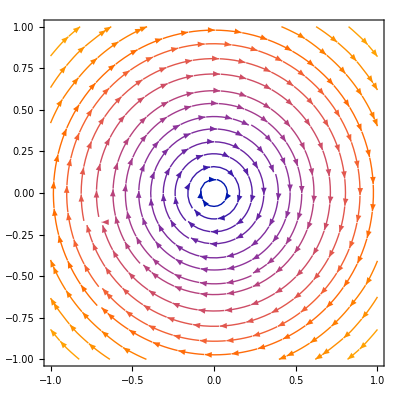

```mathematica
StreamPlot[ξ1,{x,-1,1},{y,-1,1},StreamPoints->30]
```

#### Орбиты точек

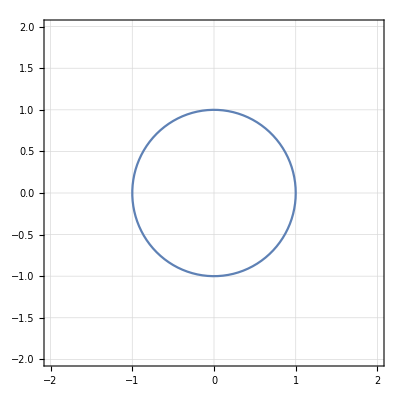

```mathematica
{x1,y1}={1,0};
Ta1[#][{x1,y1}]&;
ListLinePlot[Array[%,100,{0,2π}],Frame->True,GridLines->Automatic,PlotRange->{{-2,2},{-2,2}},AspectRatio->1]
```

#### Итог

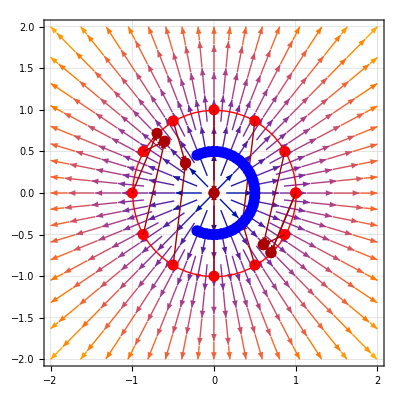

```mathematica
ClearAll[T1];
T1[a_][{x_,y_}]:={{x Cos[a],y Sin[a]},{-x Sin[a],y Cos[a]}};
{x1,y1}={1,0};
a1=0.8;
P={Cos[#],Sin[#]}&/@Range[0,2π,π/6];
P1=T1[a1][{x1,y1}].#&/@P;
Orb=(T1[a2][{x1,y1}].P⟦3⟧/.{a2->#})&/@Range[-2,2,0.1];
Show[
StreamPlot[{x,y},{x,-2,2},{y,-2,2},Frame->True,GridLines->Automatic,PlotRange->{{-2,2},{-2,2}}],Graphics[{Red, Circle[],PointSize[0.02],Point[P],Darker[Red],Point[P1],
MapThread[Arrow[{#1,#2}]&,{P,P1}],Blue,Point[Orb]}]
]
```

### Преобразование Лоренца

#### Векторное поле

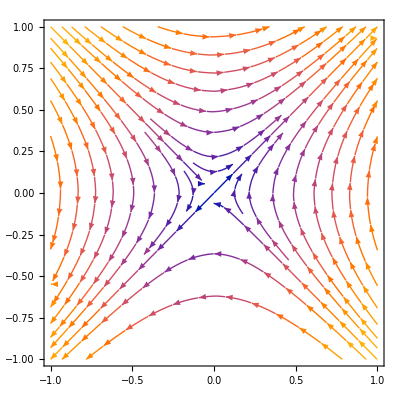

```mathematica
StreamPlot[ξ2,{x,-1,1},{y,-1,1},StreamPoints->30]
```

#### Орбиты точек

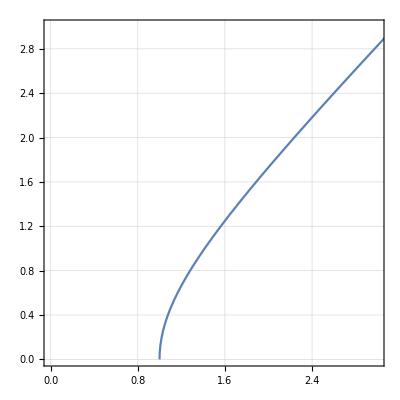

```mathematica
{x1,y1}={1,0};
Ta2[#][{x1,y1}]&;
ListLinePlot[Array[%,100,{0,2π}],Frame->True,GridLines->Automatic,PlotRange->{{0,3},{0,3}},AspectRatio->1]
```

#### Итог

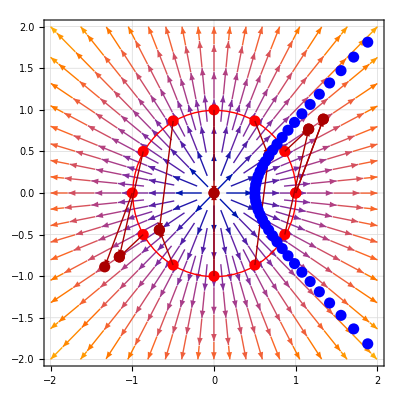

```mathematica
ClearAll[T2];
T2[a_][{x_,y_}]:={{x Cosh[a],y Sinh[a]},{x Sinh[a],y Cosh[a]}};
{x1,y1}={1,0};
a1=0.8;
P={Cos[#],Sin[#]}&/@Range[0,2π,π/6];
P1=T2[a1][{x1,y1}].#&/@P;
Orb=(T2[a2][{x1,y1}].P⟦3⟧/.{a2->#})&/@Range[-2,2,0.1];
Show[
StreamPlot[{x,y},{x,-2,2},{y,-2,2},Frame->True,GridLines->Automatic,PlotRange->{{-2,2},{-2,2}}],Graphics[{Red, Circle[],PointSize[0.02],Point[P],Darker[Red],Point[P1],
MapThread[Arrow[{#1,#2}]&,{P,P1}],Blue,Point[Orb]}]
]
```

### Неоднородное растяжение

#### Векторное поле

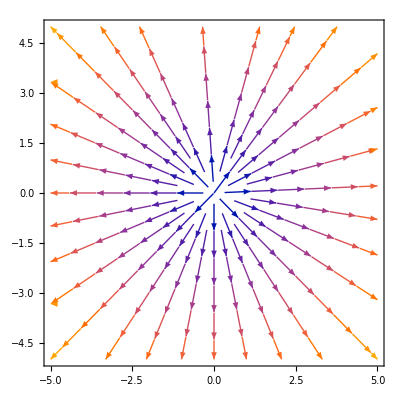

```mathematica
StreamPlot[ξ3/.{k->1},{x,-5,5},{y,-5,5},StreamPoints->30]
```

#### Орбиты точек

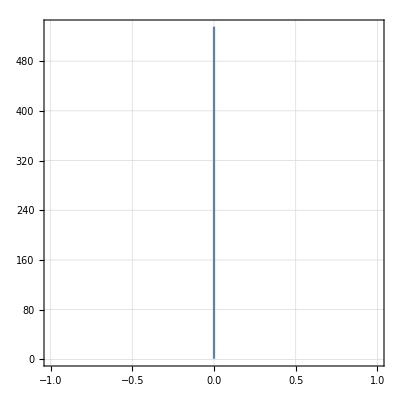

```mathematica
{x1,y1}={0,1};
Ta3[#][{x1,y1}]/.{k->1}&;
ListLinePlot[Array[%,100,{0,2π}],Frame->True,GridLines->Automatic,AspectRatio->1]
```

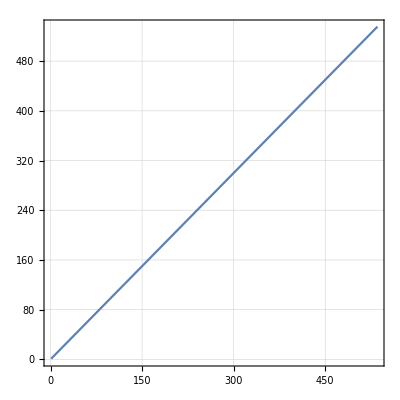

```mathematica
{x1,y1}={1,1};
Ta3[#][{x1,y1}]/.{k->1}&;
ListLinePlot[Array[%,100,{0,2π}],Frame->True,GridLines->Automatic,AspectRatio->1]
```

#### Итог

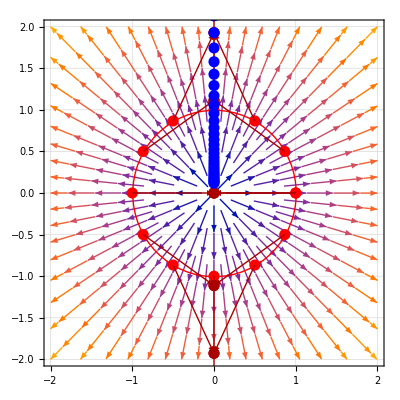

```mathematica
ClearAll[T3];
T3[a_][{x_,y_}]:={{x ⅇ^a,0},{0,y ⅇ^a}};
{x1,y1}={0,1};
a1=0.8;
P={Cos[#],Sin[#]}&/@Range[0,2π,π/6];
P1=T3[a1][{x1,y1}].#&/@P;
Orb=(T3[a2][{x1,y1}].P⟦3⟧/.{a2->#})&/@Range[-2,2,0.1];
Show[
StreamPlot[{x,y},{x,-2,2},{y,-2,2},Frame->True,GridLines->Automatic,PlotRange->{{-2,2},{-2,2}}],Graphics[{Red, Circle[],PointSize[0.02],Point[P],Darker[Red],Point[P1],
MapThread[Arrow[{#1,#2}]&,{P,P1}],Blue,Point[Orb]}]
]
```

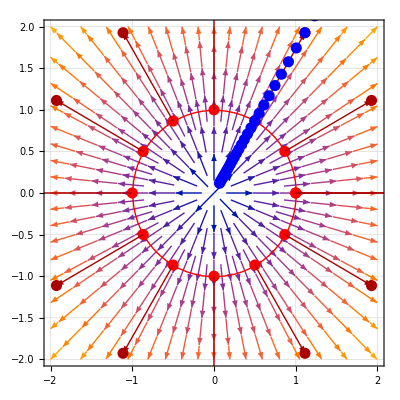

```mathematica
ClearAll[T3];
T3[a_][{x_,y_}]:={{x ⅇ^a,0},{0,y ⅇ^a}};
{x1,y1}={1,1};
a1=0.8;
P={Cos[#],Sin[#]}&/@Range[0,2π,π/6];
P1=T3[a1][{x1,y1}].#&/@P;
Orb=(T3[a2][{x1,y1}].P⟦3⟧/.{a2->#})&/@Range[-2,2,0.1];
Show[
StreamPlot[{x,y},{x,-2,2},{y,-2,2},Frame->True,GridLines->Automatic,PlotRange->{{-2,2},{-2,2}}],Graphics[{Red, Circle[],PointSize[0.02],Point[P],Darker[Red],Point[P1],
MapThread[Arrow[{#1,#2}]&,{P,P1}],Blue,Point[Orb]}]
]
```

### Преобразование Буравчика

#### Векторное поле

```mathematica
VectorPlot3D[ξ4,{x,-1,1},{y,-1,1},{z,-1,1},PlotLegends->Automatic, VectorPoints->5]
```

-Graphics3D-

#### Орбиты точек

```mathematica
{x1,y1,z1}={0,1,1};
Ta4[#][{x1,y1,z1}]&;
ListPlot3D[Array[%,100,{0,2π}],Mesh->All,ColorFunction->"SouthwestColors"]
```

-Graphics3D-

#### Итог

```mathematica
{x1,y1,z1}={1,0,0};
Ta4[#][{x1,y1,z1}]&;
Show[ParametricPlot3D[{Cos[x],Sin[y],Sin[x]},{x,0,2Pi},{y,0,2Pi}],
ListPlot3D[Array[%,100,{0,2π}],Mesh->All,ColorFunction->"SouthwestColors"]]
```

-Graphics3D-